# Chapter 12 Examples+

## Ex 12.1

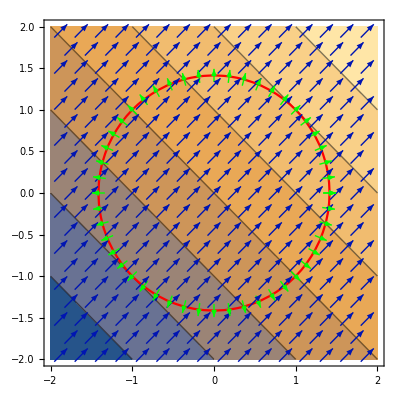

```mathematica
f[{x1_,x2_}]:= x1+x2
df[{x1_,x2_}]:={1,1}
c1[{x1_,x2_}]:= x1^2+x2^2-2
dc1[{x1_,x2_}]:={2x1,2x2}
points=Table[√2{Cos[θ],Sin[θ]},{θ,0, 2π,π/24}];
Show[
ContourPlot[f[{x1,x2}],{x1,-2,2},{x2,-2,2}],
ContourPlot[c1[{x1,x2}]==0,{x1,-2,2},{x2,-2,2},ContourStyle->Red],
VectorPlot[df[{x1,x2}],{x1,-2,2},{x2,-2,2}],
VectorPlot[dc1[{x1,x2}],{x1,-2,2},{x2,-2,2},VectorPoints->points,VectorColorFunction->None,VectorStyle->Green]
]
```

Lets identify in words where the max and min are.

## Ex 12.2

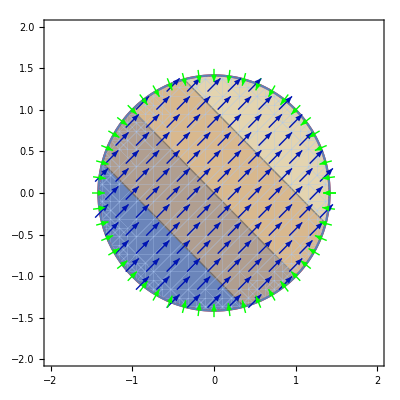

```mathematica
f[{x1_,x2_}]:= x1+x2
df[{x1_,x2_}]:={1,1}
c1[{x1_,x2_}]:= 2-(x1^2+x2^2)
dc1[{x1_,x2_}]:=-{2x1,2x2}
points=Table[√2{Cos[θ],Sin[θ]},{θ,0, 2π,π/24}];
Show[
ContourPlot[f[{x1,x2}],{x1,-2,2},{x2,-2,2},
RegionFunction->Function[{x1,x2},c1[{x1,x2}]>0]],
ContourPlot[c1[{x1,x2}]==0,{x1,-2,2},{x2,-2,2},ContourStyle->Red],
VectorPlot[df[{x1,x2}],{x1,-2,2},{x2,-2,2},RegionFunction->Function[{x1,x2},c1[{x1,x2}]>0]],
VectorPlot[dc1[{x1,x2}],{x1,-2,2},{x2,-2,2},VectorPoints->points,VectorColorFunction->None,VectorStyle->Green]
]
```

## Ex 12.3

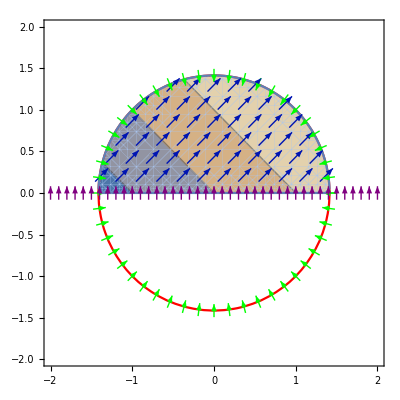

```mathematica
f[{x1_,x2_}]:= x1+x2
df[{x1_,x2_}]:={1,1}
c1[{x1_,x2_}]:= 2-(x1^2+x2^2)
c2[{x1_,x2_}]:= x2
dc1[{x1_,x2_}]:=-{2x1,2x2}
dc2[{x1_,x2_}]:={0,1}
c1points=Table[√2{Cos[θ],Sin[θ]},{θ,0, 2π,π/24}];
c2points=Table[{x1,0},{x1,-2.0,2,0.1}];
Show[
ContourPlot[f[{x1,x2}],{x1,-2,2},{x2,-2,2},
RegionFunction->Function[{x1,x2},And[c1[{x1,x2}]>0,c2[{x1,x2}]>0]]],
ContourPlot[c1[{x1,x2}]==0,{x1,-2,2},{x2,-2,2},ContourStyle->Red],
VectorPlot[df[{x1,x2}],{x1,-2,2},{x2,-2,2},RegionFunction->Function[{x1,x2},And[c1[{x1,x2}]>0,c2[{x1,x2}]>0]]],
VectorPlot[dc1[{x1,x2}],{x1,-2,2},{x2,-2,2},VectorPoints->c1points,VectorColorFunction->None,VectorStyle->Green],
VectorPlot[dc2[{x1,x2}],{x1,-2,2},{x2,-2,2},VectorPoints->c2points,VectorColorFunction->None,VectorStyle->Purple]
]
```

## Three Constraints

Not all active at min!

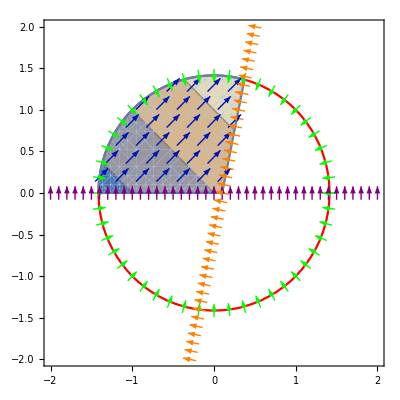

```mathematica
f[{x1_,x2_}]:= x1+x2
df[{x1_,x2_}]:={1,1}
c1[{x1_,x2_}]:= 2-(x1^2+x2^2)
c2[{x1_,x2_}]:= x2
c3[{x1_,x2_}]:= 0.1-x1+0.2x2
dc1[{x1_,x2_}]:=-{2x1,2x2}
dc2[{x1_,x2_}]:={0,1}
dc3[{x1_,x2_}]:={-1,0.2}
c1points=Table[√2{Cos[θ],Sin[θ]},{θ,0, 2π,π/24}];
c2points=Table[{x1,0},{x1,-2.0,2,0.1}];
c3points=Table[{0.1+0.2 x2,x2},{x2,-2.0,2,0.1}];
Show[
ContourPlot[f[{x1,x2}],{x1,-2,2},{x2,-2,2},
RegionFunction->Function[{x1,x2},
And[c1[{x1,x2}]>0,c2[{x1,x2}]>0,c3[{x1,x2}]>0]]],
ContourPlot[c1[{x1,x2}]==0,{x1,-2,2},{x2,-2,2},ContourStyle->Red],
VectorPlot[df[{x1,x2}],{x1,-2,2},{x2,-2,2},RegionFunction->Function[{x1,x2},
And[c1[{x1,x2}]>0,c2[{x1,x2}]>0,c3[{x1,x2}]>0]]],
VectorPlot[dc1[{x1,x2}],{x1,-2,2},{x2,-2,2},VectorPoints->c1points,VectorColorFunction->None,VectorStyle->Green],
VectorPlot[dc2[{x1,x2}],{x1,-2,2},{x2,-2,2},VectorPoints->c2points,VectorColorFunction->None,VectorStyle->Purple],
VectorPlot[dc3[{x1,x2}],{x1,-2,2},{x2,-2,2},VectorPoints->c3points,VectorColorFunction->None,VectorStyle->Orange]
]
```

## Linearization of Constraints: Constraint Qualifications

The linearization of a set of constraints at a point does not always look similar to the original.  Constraint Qualifications make sure the active constraints are well represented by the linearization. There are several possibilities the easiest to understand and the most common condition is LICQ.

LICQ: Active set constraint gradients are linearly independent

If there are two many constraints active at a corner then LICQ will not hold.
At a cusp there are two constraints with opposite directions and LICQ will not hold.

Assuming that LICQ holds allows us to perform standard linear algebra.

As an example, if we have two equality constraint c_1(x) and c_2(x) and three active inequality constraints c_3(x),c_4(x), and c_5(x) which satisfy LICQ at a point x^*  then we can eliminate 5 variables in the problem with the linearized constraints by “eliminating” variables using the equations
	c_1(x^*)+∇c_1(x^*).(x-x^*) | = | 0
c_2(x^*)+∇c_2(x^*).(x-x^*) | = | 0
c_3(x^*)+∇c_3(x^*).(x-x^*) | = | 0
c_4(x^*)+∇c_4(x^*).(x-x^*) | = | 0
c_5(x^*)+∇c_5(x^*).(x-x^*) | = | 0
This is the under-determined system
	A.x | = | b 
with A=(∇c_1
∇c_2
∇c_3
∇c_4
∇c_5) and b=(∇c_1.x^*
∇c_2.x^*
∇c_3.x^*
∇c_4.x^*
∇c_5.x^*).
As a linear algebra question, how would you choose which p variables to eliminate from the undetermined system
	A.x=b 
with A∈ℝ^(p×n) where n>p.

A potential advantage of the elliptical constraint problem is that it avoids these sorts of questions.

### LICQ Examples

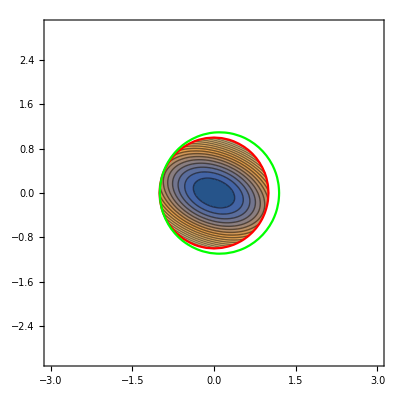

```mathematica
Clear[f]
c1[{x_,y_}]:=1-(x^2+y^2)
c2[{x_,y_}]:=1.2-((x-0.1)^2+y^2)
f[{x_,y_}]:= Sin[x y]+x^2-0.1 x y +2 y^2
Show[
ContourPlot[f[{x,y}],{x,-3,3},{y,-3,3},
RegionFunction->Function[{x,y},And[c1[{x,y}]>0,c2[{x,y}]>0]],
Contours->200],
ContourPlot[{c1[{x,y}]==0,c2[{x,y}]==0},
{x, -2,2},{y,-2,2},ContourStyle->{Red, Green}] 
]
```